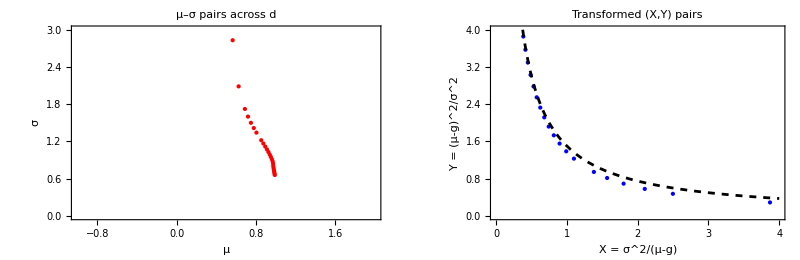

```mathematica
(*---Sweep over d,collect solutions,and plot in two coordinate systems---*)ClearAll[wTrunc,cOfSigma,Fsigma,solveForSigma]

g=-0.5;

(*truncated-sum w(D,c) with k0 cutoff*)
wTrunc[d_?NumericQ,c_?NumericQ]:=Module[{kmin,k0,tail,pmf},kmin=c-d Sqrt[c];
k0=Max[0,Ceiling[kmin]];
tail=SurvivalFunction[PoissonDistribution[c],k0-1];
pmf=If[k0>0,PDF[PoissonDistribution[c],k0-1],0];
 (d tail+Sqrt[c] pmf)];

wSum[d_,c_]:= Sum[(d+u/Sqrt[c])c^u Exp[-c]/u!,{u,Max[Ceiling[-d Sqrt[c]],0],Infinity}];

(*c(sigma)*)
cOfSigma[d_,σ_]:=((d σ-g)^2)/σ^2;
cOfSigma2[d_,σ_] :=((d σ-g)^2)/(1+σ);

(*scalar equation F(sigma)=0*)
Fsigma[d_,σ_?NumericQ]:=Module[{c,wv},c=cOfSigma[d,σ];
If[c<=0,Return[Indeterminate]];
wv=wTrunc[d,c];
If[!NumericQ[wv]||wv==0,Indeterminate,σ-1/wv]];

(*root solver wrapper*)
solveForSigma[d_?NumericQ,σguess_:0.1]:=Quiet@Module[{sol},sol=Check[FindRoot[Fsigma[d,σ]==0,{σ,σguess},WorkingPrecision->30,MaxIterations->50],$Failed];
If[sol===$Failed,Missing["NoRoot"],{σ/. sol,d (σ/. sol)}]];

(*sweep D values*)
dValues=Range[-1.5,1.5,0.05];
results=Table[{d,solveForSigma[d]},{d,dValues}];

(*extract valid (mu,sigma) pairs*)
pairs=Cases[results,{d_,{σ_?NumericQ,μ_?NumericQ}}:>{μ,σ}];

(*transformed coordinates*)
transPairs=Cases[pairs,{μ_,σ_}:>{σ^2/(μ-g),(μ-g)^2/σ^2}];

(*plot 1:mu-sigma pairs*)
p1=Show[ListPlot[pairs,PlotStyle->{Red,PointSize[Medium]},Frame->True,FrameLabel->{"μ","σ"},AspectRatio->1/GoldenRatio,PlotLabel->"μ–σ pairs across d",PlotRange->{{-1,2},{0,3}}],Plot[,{x,0.001,4},PlotStyle->{Dashed,Black}]];

(*plot 2:transformed coordinates with XY=1 line*)
p2=Show[ListPlot[transPairs,PlotStyle->{Blue,PointSize[Medium]},Frame->True,FrameLabel->{"X = σ^2/(μ-g)","Y = (μ-g)^2/σ^2"},AspectRatio->1/GoldenRatio,PlotLabel->"Transformed (X,Y) pairs"],Plot[(1-g)/x,{x,0.001,4},PlotStyle->{Dashed,Black}],PlotRange->{{0,4},{0,4}}];

(*show side by side*)
GraphicsRow[{p1,p2}]
```

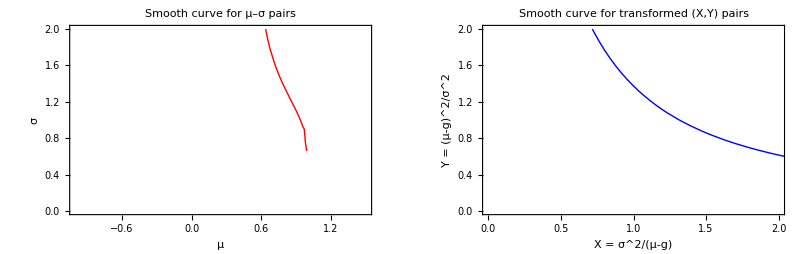

```mathematica
(*sort by first coordinate to avoid loops*)pairsSorted=SortBy[pairs,First];
transSorted=SortBy[transPairs,First];

(*build interpolation functions*)
interp1=Interpolation[pairsSorted,InterpolationOrder->3];
interp2=Interpolation[transSorted,InterpolationOrder->3];

(*plot them smoothly*)
plot1smooth=Plot[interp1[x],{x,Min[pairsSorted[[All,1]]],Max[pairsSorted[[All,1]]]},PlotStyle->{Red,Thick},PlotRange->{{-1,1.5},{0,2}},Frame->True,FrameLabel->{"μ","σ"},AspectRatio->1/GoldenRatio,PlotLabel->"Smooth curve for μ–σ pairs"];

plot2smooth=Plot[interp2[x],{x,Min[transSorted[[All,1]]],Max[transSorted[[All,1]]]},PlotStyle->{Blue,Thick},PlotRange->{{0,2},{0,2}},Frame->True,FrameLabel->{"X = σ^2/(μ-g)","Y = (μ-g)^2/σ^2"},AspectRatio->1/GoldenRatio,PlotLabel->"Smooth curve for transformed (X,Y) pairs"];

GraphicsRow[{plot1smooth,plot2smooth}]
```

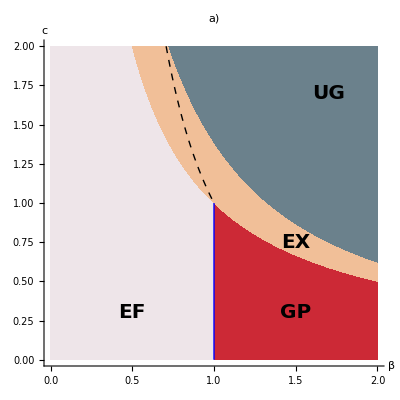

```mathematica
ga=0.5;
PhasePlot2=Show[Graphics[{Thick,Blue,Line[{{1,0},{1,1}}]}],RegionPlot[x<1&&y x <1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#EEE5E9"],BoundaryStyle->None],(*Solid Phase*)RegionPlot[x>1&&x y<1,{x,0,2},{y,0,2},PlotStyle->RGBColor["#CC2936"],BoundaryStyle->None],(*Liquid Phase*)RegionPlot[y>interp2[x],{x,0,2},{y,0,2},PlotStyle->RGBColor["#6B818C"],BoundaryStyle->None],
(*RegionPlot[x <1&&y x^2 >1,{x,0,2},{y,0,2},PlotStyle->LightBlue,BoundaryStyle->Black,PlotPoints->100],*)
RegionPlot[y x >1&&y<interp2[x],{x,0,2},{y,0,2},PlotStyle->RGBColor["#F1BF98"],BoundaryStyle->None,PlotPoints->100],
(*Gas Phase*)(*Boundary Lines*)

Graphics[{Text[Style["EF",20,Bold,Black],{0.5,0.3}],(*Solid Region*)Text[Style["GP",20,Bold,Black],{1.5,0.3}],(*Liquid Region*)
Text[Style["UG",20,Bold,Black],{1.7,1.7}]  (*Gas Region*),
(*Text[Style["MA",16,Bold,Black],{0.9,1.7}]  (*Gas Region*),*)
Text[Style["EX",20,Bold,Black],{1.5,0.75}]  (*Gas Region*)}],
AxesLabel->{"β","c"}
];

(*Show the phase diagram*)


(*Define the boundary lines*)
BoundaryLines={(*{Dashed,Black,Line[{{0,1},{1,1}}]},*){Dashed,Black,Line[Table[{x,1/x^2},{x,1/Sqrt[2],1,0.01}]]}};

(*Show the phase diagram with boundaries*)
Show[PhasePlot2,Graphics[BoundaryLines],Axes->True,AxesLabel->{Style["β",23,Black],Style["c",23,Black]},LabelStyle->{Bold,13},PlotRange->{{0,2},{0,2}},PlotLabel->"a)"]
```

0.5

InterpolatingFunction::dmval: Input value {1.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.03947} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

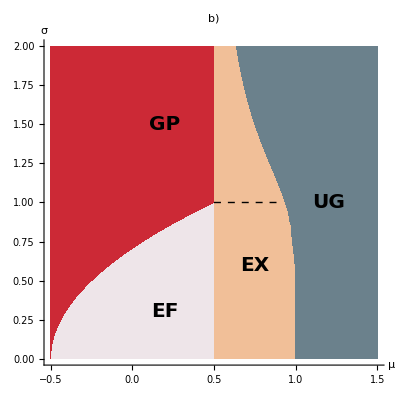

```mathematica
g=0.5
PhasePlot2=Show[(*Gas Phase*)(*Boundary Lines*)
Graphics[{{Thick,Dashed,Black,Table[Line[{{x,x^2}}],{x,0,1,0.03}]}},Axes->False],

RegionPlot[x<1-g&&y^2/(x+g)<1,{x,-g,1.5},{y,0,2},PlotStyle->RGBColor["#EEE5E9"],BoundaryStyle->None],(*Solid Phase*)RegionPlot[y^2/(x+g)>1&&x <1-g,{x,-g,1.5},{y,0,2},PlotStyle->RGBColor["#CC2936"],BoundaryStyle->None],(*Liquid Phase*)RegionPlot[x >1-g&&y<2,{x,-g,1.5},{y,0,2},PlotStyle->RGBColor["#F1BF98"],BoundaryStyle->None],RegionPlot[y>interp1[x]||x>1,{x,-1,1.5},{y,0,2},PlotStyle->RGBColor["#6B818C"],BoundaryStyle->None],
Graphics[{Text[Style["EF",20,Bold,Black],{0.2,0.3}],(*Solid Region*)Text[Style["GP",20,Bold,Black],{0.2,1.5}],(*Liquid Region*)
Text[Style["EX",20,Bold,Black],{0.75,0.6}]  ,Text[Style["UG",20,Bold,Black],{1.2,1}]  (*Gas Region*)}]
];

(*Show the phase diagram with boundaries*)
Show[PhasePlot2,Graphics[{(*{Thick,Dashed,Black,Table[Line[{{x,(x+g)^2}}],{x,-g,0.75,0.03}]},*){Thick,Dashed,Black,Line[{{g,1},{0.92,1}}]}},Axes->False],Axes->True,AxesLabel->{Style["μ",23,Black],Style["σ",23,Black]},LabelStyle->{Bold,14},PlotRange->Full,PlotLabel->"b)"]
```